## Prior

```mathematica
dataRoot=FileNameJoin[{$HomeDirectory,"Google Drive","Shared drives","SteelDrums","2DCase2","Prior"}]
```

/Users/harrihakula/Google Drive/Shared drives/SteelDrums/2DCase2/Prior

```mathematica
DirectoryQ[dataRoot]
```

True

```mathematica
priorMAT=FileNameJoin[{dataRoot,"prior.mat"}]
```

/Users/harrihakula/Google Drive/Shared drives/SteelDrums/2DCase2/Prior/prior.mat

```mathematica
Get["/Users/harrihakula/Workarea/SteelDrums/2DCase1/Prior/coeff.mma"];
Get["/Users/harrihakula/Workarea/SteelDrums/2DCase1/Prior/pd.mma"];
```

```mathematica
pd//Dimensions
```

{10000,65,200,3}

```mathematica
xs=pd[[1,All,1,1]]
ys=pd[[1,1,All,2]]
```

{-1.,-0.96875,-0.9375,-0.90625,-0.875,-0.84375,-0.8125,-0.78125,-0.75,-0.71875,-0.6875,-0.65625,-0.625,-0.59375,-0.5625,-0.53125,-0.5,-0.46875,-0.4375,-0.40625,-0.375,-0.34375,-0.3125,-0.28125,-0.25,-0.21875,-0.1875,-0.15625,-0.125,-0.09375,-0.0625,-0.03125,0.,0.03125,0.0625,0.09375,0.125,0.15625,0.1875,0.21875,0.25,0.28125,0.3125,0.34375,0.375,0.40625,0.4375,0.46875,0.5,0.53125,0.5625,0.59375,0.625,0.65625,0.6875,0.71875,0.75,0.78125,0.8125,0.84375,0.875,0.90625,0.9375,0.96875,1.}

{0.,0.0315738,0.0631476,0.0947214,0.126295,0.157869,0.189443,0.221017,0.25259,0.284164,0.315738,0.347312,0.378886,0.410459,0.442033,0.473607,0.505181,0.536755,0.568328,0.599902,0.631476,0.66305,0.694624,0.726197,0.757771,0.789345,0.820919,0.852492,0.884066,0.91564,0.947214,0.978788,1.01036,1.04194,1.07351,1.10508,1.13666,1.16823,1.1998,1.23138,1.26295,1.29453,1.3261,1.35767,1.38925,1.42082,1.45239,1.48397,1.51554,1.54712,1.57869,1.61026,1.64184,1.67341,1.70498,1.73656,1.76813,1.79971,1.83128,1.86285,1.89443,1.926,1.95758,1.98915,2.02072,2.0523,2.08387,2.11544,2.14702,2.17859,2.21017,2.24174,2.27331,2.30489,2.33646,2.36803,2.39961,2.43118,2.46276,2.49433,2.5259,2.55748,2.58905,2.62063,2.6522,2.68377,2.71535,2.74692,2.77849,2.81007,2.84164,2.87322,2.90479,2.93636,2.96794,2.99951,3.03108,3.06266,3.09423,3.12581,3.15738,3.18895,3.22053,3.2521,3.28367,3.31525,3.34682,3.3784,3.40997,3.44154,3.47312,3.50469,3.53627,3.56784,3.59941,3.63099,3.66256,3.69413,3.72571,3.75728,3.78886,3.82043,3.852,3.88358,3.91515,3.94672,3.9783,4.00987,4.04145,4.07302,4.10459,4.13617,4.16774,4.19931,4.23089,4.26246,4.29404,4.32561,4.35718,4.38876,4.42033,4.45191,4.48348,4.51505,4.54663,4.5782,4.60977,4.64135,4.67292,4.7045,4.73607,4.76764,4.79922,4.83079,4.86236,4.89394,4.92551,4.95709,4.98866,5.02023,5.05181,5.08338,5.11495,5.14653,5.1781,5.20968,5.24125,5.27282,5.3044,5.33597,5.36755,5.39912,5.43069,5.46227,5.49384,5.52541,5.55699,5.58856,5.62014,5.65171,5.68328,5.71486,5.74643,5.778,5.80958,5.84115,5.87273,5.9043,5.93587,5.96745,5.99902,6.03059,6.06217,6.09374,6.12532,6.15689,6.18846,6.22004,6.25161,6.28319}

```mathematica
Length[xs]
Length[ys]
```

65

200

```mathematica
x10=pd[[All,10,All,{2,3}]];
x30=pd[[All,30,All,{2,3}]];
```

```mathematica
y10=pd[[All,All,10,{1,3}]];
y80=pd[[All,All,80,{1,3}]];
```

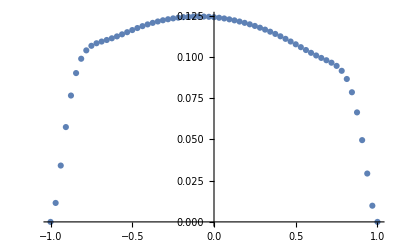

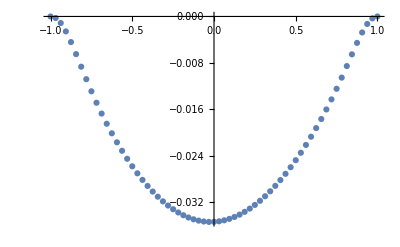

```mathematica
ListPlot[y10[[2308]]]
ListPlot[y80[[2308]]]
```

```mathematica
Export[priorMAT,{
"a0"->u0,
"a1"->u1,
"xs"->xs,
"ys"->ys,
"x10"->x10,
"x30"->x30,
"y10"->y10,
"y80"->y80
},"Header"->"Prior data","Version"->"7.3"];
```

```mathematica
xs=loc[[All,1]]
ys=loc[[All,2]]
```

{-2.0944,-2.0944,-2.0944,-2.0944,-2.0944,-0.486199,-0.560999,-0.44968,-0.44968,-0.523599,-0.523599,-0.523599,-0.523599,-0.523599,-0.523599,-0.523599,-0.523599,-0.0373999,-0.0373999,-0.0373999,-0.0373999,-1.38778×10^-17,1.38778×10^-17,0.,0.,-1.38778×10^-17,-1.38778×10^-17,-1.38778×10^-17,-1.38778×10^-17,1.46608,1.46608,1.41372,1.41372,1.41372,1.46608,1.46608,1.46608,1.46608,1.46608,1.46608,1.41372,1.41372,1.41159,1.46608,1.46608,1.46608,2.72271,2.72271,2.67035,2.67035,2.67035,2.72271,2.72271,2.72271,2.72271,2.72271,2.72271,2.67035,2.67035,2.67035,2.72271,2.72271,2.72271}

{1.0472,2.0944,3.14159,4.18879,5.23599,0.448799,0.897598,1.38292,1.83171,2.39825,2.84704,3.29584,3.74464,4.33374,4.78254,5.23134,5.68014,0.448799,0.897598,1.3464,1.7952,2.39825,2.84704,3.29584,3.74464,4.33374,4.78254,5.23134,5.68014,0.213199,0.527358,0.942478,1.25664,1.5708,1.98592,2.30008,2.61423,3.04063,3.35479,3.66895,4.08407,4.39823,4.71452,5.12751,5.44167,5.75583,0.213199,0.527358,0.942478,1.25664,1.5708,1.98592,2.30008,2.61423,3.04063,3.35479,3.66895,4.08407,4.39823,4.71239,5.12751,5.44167,5.75583}

```mathematica
Length[xs]
Length[ys]
```

63

63

```mathematica
Export[priorMAT,{
"a1"->u1,
"a2"->u2,
"a3"->u3,
"xs"->xs,
"ys"->ys,
"data"->resTable
},"Header"->"Prior data","Version"->"7.3"];
```

## Observed

```mathematica
dataRoot=FileNameJoin[{$HomeDirectory,"Google Drive","Shared drives","SteelDrums","2DCase2","Observed"}]
```

/Users/harrihakula/Google Drive/Shared drives/SteelDrums/2DCase2/Observed

```mathematica
DirectoryQ[dataRoot]
```

True

```mathematica
observedMAT=FileNameJoin[{dataRoot,"observed.mat"}]
```

/Users/harrihakula/Google Drive/Shared drives/SteelDrums/2DCase2/Observed/observed.mat

```mathematica
xs=loc[[All,1]]
ys=loc[[All,2]]
```

{-2.0944,-2.0944,-2.0944,-2.0944,-2.0944,-0.486199,-0.560999,-0.44968,-0.44968,-0.523599,-0.523599,-0.523599,-0.523599,-0.523599,-0.523599,-0.523599,-0.523599,-0.0373999,-0.0373999,-0.0373999,-0.0373999,-1.38778×10^-17,1.38778×10^-17,0.,0.,-1.38778×10^-17,-1.38778×10^-17,-1.38778×10^-17,-1.38778×10^-17,1.46608,1.46608,1.41372,1.41372,1.41372,1.46608,1.46608,1.46608,1.46608,1.46608,1.46608,1.41372,1.41372,1.41159,1.46608,1.46608,1.46608,2.72271,2.72271,2.67035,2.67035,2.67035,2.72271,2.72271,2.72271,2.72271,2.72271,2.72271,2.67035,2.67035,2.67035,2.72271,2.72271,2.72271}

{1.0472,2.0944,3.14159,4.18879,5.23599,0.448799,0.897598,1.38292,1.83171,2.39825,2.84704,3.29584,3.74464,4.33374,4.78254,5.23134,5.68014,0.448799,0.897598,1.3464,1.7952,2.39825,2.84704,3.29584,3.74464,4.33374,4.78254,5.23134,5.68014,0.213199,0.527358,0.942478,1.25664,1.5708,1.98592,2.30008,2.61423,3.04063,3.35479,3.66895,4.08407,4.39823,4.71452,5.12751,5.44167,5.75583,0.213199,0.527358,0.942478,1.25664,1.5708,1.98592,2.30008,2.61423,3.04063,3.35479,3.66895,4.08407,4.39823,4.71239,5.12751,5.44167,5.75583}

```mathematica
Length[xs]
Length[ys]
```

63

63

```mathematica
Export[observedMAT,{
"a1"->a1,
"a2"->a2,
"a3"->a3,
"xs"->xs,
"ys"->ys,
"data"->obsTable
},"Header"->"Prior data","Version"->"7.3"];
```